```mathematica
(* 1.naloga *)
(*Zavarovalni agent predstavlja zavarovalni produkt strankam na domu.Pri posameznem obisku uspešno proda zavarovalno polico z verjetnostjo 6/25. Neki dan je obiskal 3 strank. *)
Clear["Global`*"]

p = 6/25;
n=3;
distX=BinomialDistribution[n,p];
```

```mathematica
(* Izračunajte pričakovano vrednost za število prodanih zavarovalnih polic. *)
Mean[distX]//N
n*p
```

0.72

18/25

```mathematica
(* Izračunajte varianco za število prodanih zavarovalnih polic. *)
Variance[distX]//N
n*p*(1-p)
```

0.5472

342/625

{0.438976,0.415872,0.131328,0.013824}

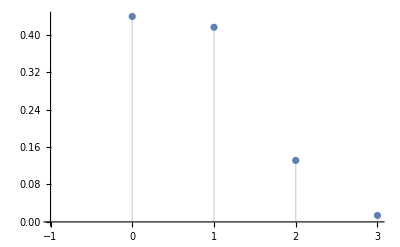

{0.438976,0.854848,0.986176,1.}

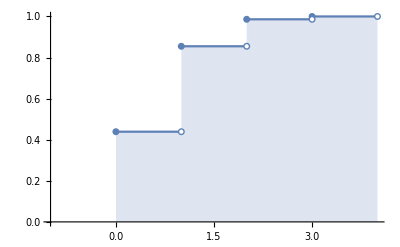

```mathematica
vfx  = Table[N[PDF[distX,k]], {k,0,3}] (* tabeliranje verjetnostne funkcije *)
ListPlot[Transpose[{Range[0,3],vfx}], AxesOrigin->{-1,0}, Filling->Axis]
pfx = Table[N[CDF[distX,k]], {k,0,3}](* tabeliranje kumulativne porazdelitvene funkcije *)
DiscretePlot[pfx[[k+1]],{k,0,3}, AxesOrigin->{-1,0}, ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
(* Da izpolni normo,mora prodati najmanj 0 polic.S kolikšno verjetnostjo bo izpolnil normo? *)
(* P(X ≥ 0)= 1 - P(X ≤ 1)*)
1-CDF[distX,0] //N
CDF[distX, 3]-CDF[distX, 0]//N
1-PDF[distX,0]
```

0.561024

0.561024

8766/15625

1-List

{0.0479085,0.060684,0.0691798,0.0736073,0.0745887,0.0728839,0.0692397,0.064316,0.0586562,0.0526839,0.0467131,0.0409638,0.0355799,0.0306462,0.0262025,0.0222567,0.0187946,0.0157874,0.0131983,0.010986,0.00910839,0.00752433,0.00619503,0.00508488,0.00416178,0.00339724,0.00276633,0.0022474,0.00182189,0.00147397,0.00119023,0.000959399,0.000772034,0.000620274,0.000497598,0.000398616}

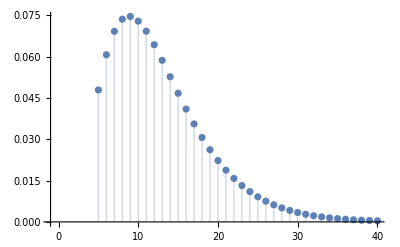

{0.0932512,0.153935,0.223115,0.296722,0.371311,0.444195,0.513435,0.577751,0.636407,0.689091,0.735804,0.776767,0.812347,0.842994,0.869196,0.891453,0.910247,0.926035,0.939233,0.950219,0.959327,0.966852,0.973047,0.978132,0.982293,0.985691,0.988457,0.990704,0.992526,0.994,0.995191,0.99615,0.996922,0.997542,0.99804,0.998438}

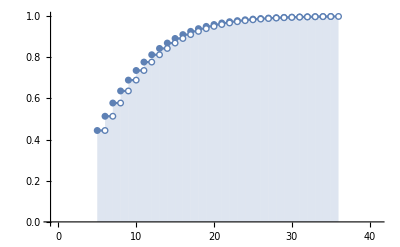

```mathematica
(* Agent se odloči,da si bo vzel dopust,ko bo prodal naslednjih 5 polic. *)
distY=PascalDistribution[n,p];

vfy  = Table[N[PDF[distY,k]], {k,5,40}] (* tabeliranje verjetnostne funkcije *)
ListPlot[Transpose[{Range[5,40],vfy}], AxesOrigin->{-1,0}, Filling->Axis]
pfy = Table[N[CDF[distY,k]], {k,5,40}](* tabeliranje kumulativne porazdelitvene funkcije *)
DiscretePlot[pfy[[k+1]],{k,5,40}, AxesOrigin->{-1,0}, ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
(* Zapišite verjetnost,da bo moral do dopusta obiskati še natanko 21 strank *)
CDF[distY, 21]//N
PDF[distY, 21]//N
```

0.910247

0.0187946

```mathematica
(* 2.naloga *)
(* Kovanec vržemo 18-krat. Slučajna spremenljivka X je število padlih grbov. *)
Clear["Global`*"]
n=18; p=0.5;
```

```mathematica
(* Poiščite njeno pričakovano vrednost in varianco *)
EX = n p
VarX=n p (1-p)
```

9.

4.5

```mathematica
(* Kolikšna je verjetnost,da bo število padlih grbov enako 3? *)
Binomial[n, 3]*p^3*(1-p)^15
```

0.480249

```mathematica
(* 3.naloga *)
(* Čas med dvema klicema v pisarno je eksponentno porazdeljena slučajna spremenljivka s povprečno vrednostjo 27 minut. *)
Clear["Global`*"]
dist=ExponentialDistribution[27];
(* Kolikšna je verjetnost,da so bili več kot trije klici v pol ure? *)
CDF[dist,3]//N
1-N[CDF[dist,3]]

Quantile[dist,0.01]
```

1.

0.

0.000372235

```mathematica
(* Kolikšna je verjetnost,da ni bilo nobenega klica v pol ure? *)
```

```mathematica
(* Določite x tako,da bo verjetnost,da ne bo nobenega klica v x urah, enaka 0.01. *)
```

```mathematica
(* Izračunajte varianco. *)
```

```mathematica
(* 4.naloga *)
(* Slučajna spremenljivka je porazdeljena po normalni porazdelitvi s parametroma mi=9 in sigma=11. Zapišite enačbo porazdelitvene funkcije za spremenljivko X.(Izrazite jo s funkcijo fi.) Izračunajte verjetnosti dogodkov 0.3mi≤ X≤ 1.2mi *)
```

```mathematica
Clear["Global`*"]
dist=NormalDistribution[9,11];

N[CDF[dist,10.8]] - N[CDF[dist,2.7]]
1-N[CDF[dist,11]]
N[Quantile[dist,0.75],8]
N[Quantile[dist,0.3],8]
```

0.281577

0.427863

16.4194

3.23159

```mathematica
(* 5.naloga *)
(* Slučajna spremenljivka ima zalogo vrednosti 1...15 in verjetnostno funkcijo *)
```

```mathematica
Clear["Global`*"]

a=a/.Flatten[N[Solve[Sum[a k^4*(15/17)^k, {k,1,15}]==1,a]]]
```

0.0000270328

```mathematica
N[EX= Sum[k*a *k^4*(15/17)^k, {k, 1,15}],7]
EX2=Sum[k^2*a* k^4*(15/17)^k, {k, 1,15}]
VarX=EX2-EX^2
StdX=Sqrt[VarX]


N[EX= Sum [k*a *k^4*(15/17)^k, {k, 1,15}],7]
```

12.2018

155.318

6.43343

2.53642

12.2018

```mathematica
(* 6.naloga *)
Clear["Global`*"]
f[x_]:=c/(1+1.7*x)^2;
a=0; b=7;

Reduce[Integrate[f[x], {x, a, b}]==1]
c=c/.Flatten[N[Solve[Integrate[f[x], {x,a,b}]]==1]]
```

c==1.84286

Solve::naqs: 0.542636 c is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Solve[0.542636 c]==1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.542636 c]==1..

Hold[c/.Solve[0.542636 c]==1.]

```mathematica
dist = ProbabilityDistribution[f[x],{x,a, b}];
CDF[dist, 0]-CDF[dist,3]//N
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.542636 c]==1..

CDF[dist,0.]-1. CDF[dist,3.]